```mathematica
vertices={{1,0,5000},{2,1000,5000},{3,3500,5000},{4,4500,5000},{5,5000,5000},{6,1000,4000},{7,2000,4000},{8,3500,4000},{9,0,3500},{10,1000,3500},{11,2000,3000},{12,3500,3000},{13,4500,3000},{14,1000,2000},{15,2000,2000},{16,3500,2000},{17,4500,2000},{18,5000,2000},{19,0,1500},{20,1000,1500},{21,3500,1000},{22,4000,1000},{23,5000,1000},{24,0,500},{25,1000,500},{26,3500,500},{27,0,0},{28,3500,0},{29,4000,0},{30,5000,0}};
```

```mathematica
aristas={{1,2,1000},{2,6,1000},{6,10,500},{9,10,1000},{1,9,1500},{2,3,2500},{3,8,1000},{7,8,1500},{6,7,1000},{3,4,1000},{4,13,2000},{12,13,1000},{8,12,1000},{4,5,500},{5,18,3000},{17,18,500},{13,17,1000},{7,11,1000},{11,15,1000},{14,15,1000},{10,14,1500},{11,12,1500},{14,20,500},{19,20,1000},{9,19,2000},{16,17,1000},{15,16,1500},{16,21,1000},{21,26,500},{25,26,2500},{20,25,1000},{18,23,1000},{22,23,1000},{21,22,500},{24,25,1000},{19,24,1000},{22,29,1000},{28,29,500},{26,28,500},{23,30,1000},{29,30,1000},{27,28,3500},{24,27,500}};

(*OBTENCION DE LOS VERTICES QUE FORMAN PARTE DE LA PERIFERIA*)
origen={1,2,3,4,5,9,18,19,23,24,27,28,29,30};
```

Generación de un grafo a partir de los vertices y aristas

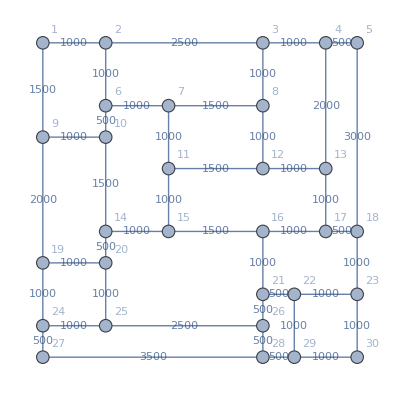

```mathematica
(*EL PRIMER ELEMENTO ES EL VERTICE Y EL SEGUNDO ES UNA BANDERA PARA SABER SI HA SIDO ANALIZAOD ANTERIORMENTE O NO*)
banderas = {{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0}};

(*INICIALIZAR LAS VARIABLES*)
conexiones={};
pesos = {};
coordenadas={};

(*OBTENER LAS CONEXIONES Y LOS PESOS*)
For[x=1,x≤Length[aristas],x++,
AppendTo[pesos,aristas[[x]][[3]] ];
AppendTo[conexiones,aristas[[x]][[1]]<->aristas[[x]][[2]] ];
]


(*OBTENER LAS COORDENADAS*)
For[x=1,x≤Length[aristas],x++,
(*SE OBTIENE EL PRIMER VERTICE DE LA ARISTA ANALIZADA*)
aux = aristas[[x]][[1]];
(*SE OBTIENE LA POSICION DE ESE VERTICE EN EL ARRAY DE BANDERAS*)
i =Position[banderas,aux][[1]][[1]];
(*SI EL VERTICE NO HA SINO ANALIZADA*)
If[  banderas[[i]][[2]]==0,
(*SE CAMBIA A ANALIZADO*)
banderas[[i]][[2]]=1;
(*SE OBTIENE LA UBICACION DEL VERTICE EN EL ARRAY DE VERTICES*)
j = Position[vertices,aux][[1]][[1]];
(*SE OBTIENEN LAS COORDENADAS DEL VERTICE SEGUN LA POSICION OBTENIDA ANTERIORMENTE*)
AppendTo[coordenadas,{vertices[[j]][[2]],vertices[[j]][[3]]  }]
];

(*EL PROCESO ANTERIOR SE REPITE CON EL SEGUNDO VERTICE DE LA ARISTA*)
aux = aristas[[x]][[2]];
i =Position[banderas,aux][[1]][[1]];
If[  banderas[[i]][[2]]==0,
banderas[[i]][[2]]=1;
j = Position[vertices,aux][[1]][[1]];
AppendTo[coordenadas,{vertices[[j]][[2]],vertices[[j]][[3]]  }]
]
]

(*SE MAPEAN LAS CONEXIONES PARA GENERAR LAS ARISTAS*)
eEdges=Map[conexiones_⟦#⟧->pesos_⟦#⟧&,Range[Length[pesos]]];
(*SE CREA AL GRAFO*)
grafo =Graph[conexiones,VertexLabels->"Name",VertexSize->Large,EdgeWeight->pesos,VertexCoordinates->coordenadas,EdgeLabels->eEdges];
grafo
```

Procesamiento de los poligonos

```mathematica
(*POLIGONOS DEL GRAFO*)
Poligonos ={{1<->2,2<->10,10<->9,9<->1},{2<->3,3<->8,8<->6,6<->2},{3<->4,4<->13,13<->12,12<->3}, {4<->5,5<->18,18<->17,17<->4},{6<->7,7<->15,15<->14,14<->6},{7<->8,8<->12,12<->11,11<->7},{9<->10,10<->20,20<->19,19<->9},{11<->13,13<->17,17<->15,15<->11},{14<->16,16<->26,26<->25,25<->14},{16<->18,18<->23,23<->21,21<->16},{19<->220,20<->25,25<->24,24<->19},{21<->22,22<->29,29<->28,28<->21},{22<->23,23<->30,30<->29,29<->22},{24<->26,26<->28,28<->27,27<->24}};
(*COORDENADAS DE X*)
xs={};
(*COORDENADAS DE Y*)
ys={};
For[x=1,x≤Length[vertices],x++,
AppendTo[xs,vertices[[x]][[2]] ];
AppendTo[ys,vertices[[x]][[3]] ]
]

(*OBTENER LAS COORDENADAS MAYOYES DEL GRAFO; PARA CONOCER LOS LIMITES*)
(*OBTENCION DE LA COORDENADA EN X MAYOR*)
maxX = Max[xs];
(*OBTENCION DE LA COORDENADA EN Y MAYOR*)
maxY = Max[ys];


(*VARIABLE CONTENEDORA DE LOS VERTICES QUE SE ENCUENTREN EN LA PERIFERIA*)
verticesPeriferia= {};
(*SE RECORRE LA LISTA DE VERTICES Y SUS COORDENADAS*)
For[x=1, x≤Length[vertices],x++,
(*SI LA COORDENADA X O Y SE ENCUENTRA EN LOS LÍMITES DEL GRAFO, ES UN VERTICE EN LA PERIFERIA*)
If[vertices[[x]][[2]]== maxX || vertices[[x]][[3]]== maxY || vertices[[x]][[3]]== 0 || vertices[[x]][[2]]== 0 ,
(*SE AGREGA EL VERTICE A LA LISTA DE VERTICES EN LA PERIFERIA*)
AppendTo[verticesPeriferia, vertices[[x]][[1]] ]
]
]


(*VERTICES DE LA PERIFERIA*)
Print["VERTICES EN LA PERIFERIA"]
verticesPeriferia
```

VERTICES EN LA PERIFERIA

{1,2,3,4,5,9,18,19,23,24,27,28,29,30}

Obtener el vertice con mayor número de conexiones

```mathematica
verticesEnPoligonos ={};
For[x=1, x≤ Length[Poligonos], x++,
AppendTo[verticesEnPoligonos, VertexList[Poligonos[[x]]]]
]
(*VARIABLE QUE CONTIENE LOS VERTICES DE CADA POLIGONO*)
Print["VERTICES EN POLIGONOS"]
verticesEnPoligonos

(*VARIABLES BANDERAS PARA OBTENER EL VERTICE CON MAYORES CONEXIONES*)
vertice =0;
cantidadConexiones =0;
contador =0;



(*SE SELECCIONA EL PRIMERO DE LOS POLIGONOS PARA ANALIZARLO*)
listaVertices = verticesEnPoligonos[[1]];
listaDePoligonos = verticesEnPoligonos;



(*OBTENER EL VERTICE CON MAYORES CONEXIONES*)
For[x=1, x≤Length[listaVertices], x++,
(*SE VERIFICA QUE SEA UN VERTICE DE LA PERIFERIA*)
If[MemberQ[verticesPeriferia,listaVertices[[x]]],
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[verticesEnPoligonos],i++,
If[MemberQ[verticesEnPoligonos[[i]],listaVertices[[x]]  ],
contador= contador +1;
]
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = listaVertices[[x]];
]
]
]

(*AGREGAR EL VERTICE A LA LISTA DE VERTICES COMPARTIDOS*)
AppendTo[verticesCompartidos, vertice];
Print["Vertice con más conexiones"]
vertice

(*ELIMINAR LOS POLIGONOS QUE CONTIENE AL VERTICE*)
For[i=1, i≤Length[verticesEnPoligonos],i++,
If[MemberQ[verticesEnPoligonos[[i]],vertice],
verticesEnPoligonos = ReplacePart[verticesEnPoligonos, i-> {0}];
]
]
(*LISTA DE POLIGONOS*)
verticesEnPoligonos
(*LISTA COMPLETA CONTENEDORA DE LOS POLIGONOS*)
listaDePoligonos



While
```

VERTICES EN POLIGONOS

{{1,2,10,9},{2,3,8,6},{3,4,13,12},{4,5,18,17},{6,7,15,14},{7,8,12,11},{9,10,20,19},{11,13,17,15},{14,16,26,25},{16,18,23,21},{19,220,20,25,24},{21,22,29,28},{22,23,30,29},{24,26,28,27}}

Vertice con más conexiones

2

{{0},{0},{3,4,13,12},{4,5,18,17},{6,7,15,14},{7,8,12,11},{9,10,20,19},{11,13,17,15},{14,16,26,25},{16,18,23,21},{19,220,20,25,24},{21,22,29,28},{22,23,30,29},{24,26,28,27}}

{{1,2,10,9},{2,3,8,6},{3,4,13,12},{4,5,18,17},{6,7,15,14},{7,8,12,11},{9,10,20,19},{11,13,17,15},{14,16,26,25},{16,18,23,21},{19,220,20,25,24},{21,22,29,28},{22,23,30,29},{24,26,28,27}}